# Machine Learning using Mathematica

## Aashita Kesarwani

## Introduction

What is Data Science?

Computation with data

What is Machine Learning?

Building systems that can learn from data, instead of explicitly programmed instructions

Common Tasks:

Classification

Methods used: Logistic Regression, Tree-based algorithms, Naive-Bayes, k-Nearest Neighbours, Deep Neural Networks, etc.

Regression

Methods used: Linear, Ridge, Lasso,  Polynomial, etc.

# Goal

Learning to train classifiers with the use of the three main functions in Mathematica:

ResourceData

Classify

Predict

## Titanic Survival Prediction

#### Import data from Wolfram data repository:

```mathematica
titanic = ResourceData["Sample Data: Titanic Survival"];
RandomSample[titanic, 5]
```

Dataset[<>]

#### Finding the number of passengers in the dataset:

```mathematica
Dimensions[titanic]
```

{1309,4}

#### What proportion of passengers survived?

```mathematica
PieChart[Counts[titanic[[All,"SurvivalStatus"]]], PlotLabel->"Titanic Passengers' survival", ChartLabels ->{"survived", "died"}, ImageSize->Small]
```

-Graphics-

## A look at the variables:

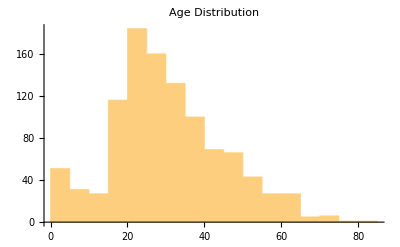

```mathematica
Histogram[titanic[All, "Age"], PlotLabel->"Age Distribution" ]
```

```mathematica
PieChart[Counts[titanic[[All,"Class"]]],ChartLabels ->{"1st", "2nd", "3rd"}, ImageSize->Small]
```

-Graphics-

```mathematica
PieChart[Counts[titanic[[All,"Sex"]]],ChartLabels ->{"female", "male"}, ImageSize->Small]
```

-Graphics-

#### Splitting the data into training and testing set:

```mathematica
SeedRandom[0];data=RandomSample@titanic;
training = data[[;;1000]];
testing = data[[1001;;]];
```

#### Training a classifier:

```mathematica
classifier=Classify[training-> "SurvivalStatus", Method->"LogisticRegression"];
ClassifierInformation[classifier]
```

Classifier information
Input type | {Nominal,Numerical,Nominal}
Classes | ,,diedsurvived
Method | LogisticRegression
Accuracy | 79.1 % ± 1.1 %
Loss | 0.453 ± 0.015
Single evaluation time | 5.44 ms/example
Batch evaluation speed | 15.7 examples/ms
Classifier memory | 313. kB
Training examples used | 1000 examples
Training time | 6.12 s
 |

### Defining a predictor function using the classifier:

```mathematica
predictor[class_,age_,sex_]:=classifier[{class,age,sex},{"Probability","survived"}];
```

### Some predictions for the probabilities of survival:

```mathematica
{predictor["2nd", 25, "female"], predictor["2nd", 25, "male"]}
```

{0.909477,0.421493}

```mathematica
{predictor["1st", 25, "female"], predictor["3rd", 25, "female"]}
```

{0.966392,0.758737}

### The performance measures of the classifier

```mathematica
cm = ClassifierMeasurements[classifier,testing -> "SurvivalStatus"];
```

#### Accuracy for the classifier on testing dataset:

```mathematica
cm["Accuracy"]
```

cm[Accuracy]

#### Confusion matrix for the classifier:

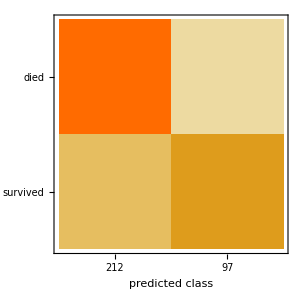

```mathematica
cm["ConfusionMatrixPlot"]
```

#### Accuracy for the classifier on training dataset:

```mathematica
ClassifierMeasurements[classifier,training -> "SurvivalStatus"]["Accuracy"]
```

0.794

## Wolfram Data Repository

Access using ResourceData

Freely available ready-to-use datasets

## Wolfram Open Cloud

Free storage of own data -- publish freely or share in a more controlled fashion

Making a Data-Backed Publication by linking to the webpage

### Training a classifier to recognize handwrittten digits:

#### Importing data from MNIST dataset:

```mathematica
RandomSample[ResourceData["MNIST","TrainingData"], 5]
```

{-Graphics-→7,-Graphics-→2,-Graphics-→1,-Graphics-→6,-Graphics-→1}

#### Training the classifier:

```mathematica
digit = Classify[
{-Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 2, -Graphics- -> 7, -Graphics- -> 5, -Graphics- -> 1, -Graphics- -> 3, -Graphics- -> 0, -Graphics- -> 3, -Graphics- -> 9, -Graphics- -> 6, -Graphics- -> 2, -Graphics- -> 8, -Graphics- -> 2, -Graphics- -> 0, -Graphics- -> 6, -Graphics- -> 6, -Graphics- -> 1, -Graphics- -> 1, -Graphics- -> 7, -Graphics- -> 8, -Graphics- -> 5, -Graphics- -> 0, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 6, -Graphics- -> 0, -Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 5, -Graphics- -> 6, -Graphics- -> 7, -Graphics- -> 5, -Graphics- -> 4, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 3, -Graphics- -> 6, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 9, -Graphics- -> 3, -Graphics- -> 0, -Graphics- -> 3, -Graphics- -> 7, -Graphics- -> 4, -Graphics- -> 4, -Graphics- -> 3, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 4, -Graphics- -> 1, -Graphics- -> 3, -Graphics- -> 7, -Graphics- -> 6, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 2, -Graphics- -> 7, -Graphics- -> 2, -Graphics- -> 5, -Graphics- -> 2, -Graphics- -> 0, -Graphics- -> 9, -Graphics- -> 8, -Graphics- -> 9, -Graphics- -> 8, -Graphics- -> 1, -Graphics- -> 6, -Graphics- -> 4, -Graphics- -> 8, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 0, -Graphics- -> 6, -Graphics- -> 7, -Graphics- -> 4, -Graphics- -> 5, -Graphics- -> 8, -Graphics- -> 4, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 5, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 9, -Graphics- -> 9, -Graphics- -> 2, -Graphics- -> 4, -Graphics- -> 7, -Graphics- -> 3, -Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 2, -Graphics- -> 9, -Graphics- -> 6}]
```

ClassifierFunction[…]

#### Testing the classifier:

```mathematica
digit[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{0,1,2,3,4,1,6,7,8,9}

```mathematica
digit[-Graphics-, "TopProbabilities"]
```

{6→0.345171,0→0.338547,4→0.298782}

## Training a classifier for image recognition

#### Importing CIFAR-10 images:

```mathematica
SeedRandom[0];imageData = RandomSample[ResourceData["CIFAR-10", "TrainingData"],80]
```

{-Graphics-→ship,-Graphics-→automobile,-Graphics-→frog,-Graphics-→airplane,-Graphics-→truck,-Graphics-→ship,-Graphics-→frog,-Graphics-→airplane,-Graphics-→bird,-Graphics-→dog,-Graphics-→frog,-Graphics-→ship,-Graphics-→airplane,-Graphics-→horse,-Graphics-→automobile,-Graphics-→bird,-Graphics-→frog,-Graphics-→deer,-Graphics-→automobile,-Graphics-→horse,-Graphics-→horse,-Graphics-→frog,-Graphics-→airplane,-Graphics-→horse,-Graphics-→horse,-Graphics-→airplane,-Graphics-→dog,-Graphics-→airplane,-Graphics-→frog,-Graphics-→cat,-Graphics-→deer,-Graphics-→ship,-Graphics-→truck,-Graphics-→frog,-Graphics-→bird,-Graphics-→dog,-Graphics-→automobile,-Graphics-→ship,-Graphics-→ship,-Graphics-→cat,-Graphics-→dog,-Graphics-→deer,-Graphics-→frog,-Graphics-→cat,-Graphics-→ship,-Graphics-→ship,-Graphics-→truck,-Graphics-→dog,-Graphics-→horse,-Graphics-→frog,-Graphics-→truck,-Graphics-→frog,-Graphics-→deer,-Graphics-→horse,-Graphics-→dog,-Graphics-→cat,-Graphics-→horse,-Graphics-→ship,-Graphics-→ship,-Graphics-→deer,-Graphics-→frog,-Graphics-→airplane,-Graphics-→bird,-Graphics-→frog,-Graphics-→cat,-Graphics-→bird,-Graphics-→dog,-Graphics-→bird,-Graphics-→dog,-Graphics-→bird,-Graphics-→automobile,-Graphics-→frog,-Graphics-→horse,-Graphics-→dog,-Graphics-→automobile,-Graphics-→airplane,-Graphics-→dog,-Graphics-→dog,-Graphics-→cat,-Graphics-→bird}

#### Training the classifier:

```mathematica
c = Classify[imageData];
```

#### Testing the classifier:

```mathematica
c[-Graphics-, {"TopProbabilities", 3}]
```

{dog→1.,cat→8.19423×10^-15,ship→3.35577×10^-20}

```mathematica
c[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{automobile,frog,bird,horse,ship}

Training  classifiers on Textual data

#### A classifier trained on word tokens with text labels - good or bad:

```mathematica
c=Classify[{{"butter","sugar","flour"}->"bad",{"flour","butter"}->"good",{"tomato","salt"}->"good"}]
```

ClassifierFunction[…]

```mathematica
c[{"butter","tomato","apple"}]
```

good

#### Another classifier train on text with labels as images of a cat and a dog :

```mathematica
c = Classify[{"this cat is adorable" -> -Graphics-, "my cat is furry" -> -Graphics-, "the dog is playful" -> -Graphics- , "the cute little dog" -> -Graphics-}]
```

```mathematica
c[{"sweet cat","loyal dog"}]
```

{-Graphics-,-Graphics-}

Training a classifier to identify the author of a writing:

#### Importing some of the writings of Shakespeare:

```mathematica
Othello=Import["http://www.gutenberg.org/cache/epub/2267/pg2267.txt"];
Hamlet=Import["http://www.gutenberg.org/cache/epub/2265/pg2265.txt"];
Macbeth=Import["http://www.gutenberg.org/cache/epub/2264/pg2264.txt"];
```

#### Importing some of the writings of Oscar Wilde:

```mathematica
TheImportanceOfBeingEarnest=Import["http://www.gutenberg.org/cache/epub/844/pg844.txt"];
ThePictureofDorianGray=Import["http://www.gutenberg.org/cache/epub/174/pg174.txt"];
AnIdealHusband=Import["http://www.gutenberg.org/files/885/885-0.txt"];
```

#### Importing some of the writings of Victor Hugo:

```mathematica
LesMiserables=Import["http://www.gutenberg.org/cache/epub/135/pg135.txt"];
NotreDamedeParis=Import["http://www.gutenberg.org/cache/epub/2610/pg2610.txt"];
TheManWhoLaughs=Import["http://www.gutenberg.org/cache/epub/12587/pg12587.txt"];
```

#### Training the classifier:

```mathematica
author=Classify[<|"William Shakespeare"->{Othello,Hamlet},"Oscar Wilde"->{TheImportanceOfBeingEarnest,ThePictureofDorianGray},"Victor Hugo"->{LesMiserables,NotreDamedeParis}|>]
```

ClassifierFunction[…]

```mathematica
author[{Macbeth,AnIdealHusband,TheManWhoLaughs}]
```

{William Shakespeare,Oscar Wilde,Victor Hugo}

## Built-in classifiers for Text Analysis:

```mathematica
Classify["Language",{"Een prettige dag","வாருங்கள்","お元気ですか","хорошего дня", "ทั้งหมดที่ดีที่สุด"}]
```

{Dutch,Tamil,Japanese,Russian,Thai}

```mathematica
Classify["FacebookTopic",{"Happy Birthday :)","Best smartphone ever!", "Love your dress!"}]
```

{SpecialOccasions,Technology,Fashion}

```mathematica
Classify["NameGender",{"Lisa","Arnold","Katrina","Mitchelle", "Harris"}]
```

{Female,Male,Female,Indeterminate,Male}

```mathematica
Classify["Sentiment",{"I love reading","I am excited for the trip","I lost my keys"}]
```

{Positive,Positive,Negative}

```mathematica
Classify["Profanity",Import["http://www.urbandictionary.com/random.php"]]
```

True

## Using Mathematics for Machine Learning:

### Pros:

Highly automated, you can start the analysis right away

Unlike most other languages/platforms, availability of in-built data repository that is very well suited for learning and teaching purposes

Free storage of own data on Wolfram Cloud

Suitable to prepare the data, visualize and analyze it as well as build a quick baseline model before building models in other frameworks such as TensorFlow

### Cons :

Lack of a clear understanding of what is happening behind the scenes

Limited scope for customization

Slow to catch up with the recent developments in certain areas like Deep Learning

Other Frameworks work better in integration with GPUs to speed up the training of models for large datasets

## References

http://blog.wolfram.com/2017/04/20/launching-the-wolfram-data-repository-data-publishing-that-really-works/

http://blog.wolfram.com/2018/08/09/citizen-data-science-with-civic-hacking-the-safe-drinking-water-data-challenge/

http://blog.wolfram.com/2017/10/10/building-the-automated-data-scientist-the-new-classify-and-predict/https://reference.wolfram.com/language/ref/Classify.html

https://www.wolfram.com/language/11/neural-networks/object-classification.html?product=mathematica

https://reference.wolfram.com/language/ref/Classify.html

## Datasets

https://datarepository.wolframcloud.com/resources/Sample-Data-Titanic-Survival

https://datarepository.wolframcloud.com/resources/MNIST

https://datarepository.wolframcloud.com/resources/CIFAR-10_1

## Github Link for the presentation

https://github.com/AashitaK/Machine-Learning-using-Mathematica

Thank you!

Questions?